```mathematica
k=(c.{{ x^2, x y/2},{ x y/2,y^2}}.Transpose[c])2/100/.α->ArcCos[b]
```

{{1/50 (b (b x^2-1/2 √(1-b^2) x y)-√(1-b^2) ((b x y)/2-√(1-b^2) y^2)),1/50 (√(1-b^2) (b x^2-1/2 √(1-b^2) x y)+b ((b x y)/2-√(1-b^2) y^2))},{1/50 (b (√(1-b^2) x^2+(b x y)/2)-√(1-b^2) (1/2 √(1-b^2) x y+b y^2)),1/50 (√(1-b^2) (√(1-b^2) x^2+(b x y)/2)+b (1/2 √(1-b^2) x y+b y^2))}}

```mathematica
ko1=Simplify[-k[[1,2]]]
```

1/100 (x y-2 b^2 x y+2 b √(1-b^2) (-x^2+y^2))

```mathematica
ko=Simplify[k[[1,1]]+k[[1,2]]]
```

1/100 (y (-x+2 y)+2 b √(1-b^2) (x^2-x y-y^2)+2 b^2 (x^2+x y-y^2))

```mathematica
ko2=Simplify[k[[2,2]]+k[[1,2]]]
```

1/100 (2 (1-b^2+b √(1-b^2)) x^2+(-1+2 b^2+2 b √(1-b^2)) x y+2 b (b-√(1-b^2)) y^2)

```mathematica
RegionPlot3D[ko2≥0&&ko≥0&&ko1≥0,{x,50,150},{y,50,150},{b,-1,1}]
```

-Graphics3D-

```mathematica
f[a_]:=MinValue[{ko+ko2+ko1/.b->a,50≤x≤150,50≤y≤150},{x,y}];
```

```mathematica
f3[a_]:=Min[f[a],f2[a],f1[a]]
```

```mathematica
f3[0.5]
```

-135.705

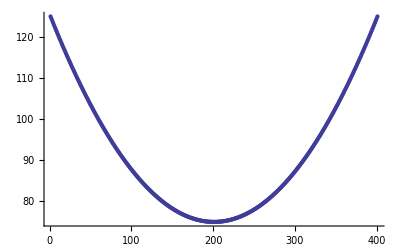

```mathematica
ListPlot[Table[f[i/200],{i,-200,200}]]
```

```mathematica
bb=1;{f[bb],f1[bb],f2[bb]}
```

{25/2,25,25/2}

```mathematica
Simplify[k/.α->π 37/60//N]
```

{{0.00256855 x^2+0.00669131 x y+0.0174314 y^2,-0.00669131 x^2-0.00743145 x y+0.00669131 y^2},{-0.00669131 x^2-0.00743145 x y+0.00669131 y^2,0.0174314 x^2-0.00669131 x y+0.00256855 y^2}}

```mathematica
π 37/60.
```

1.93732

```mathematica
(k/.α->ArcCos[-0.7614944037382076])[[1,2]]/.x->150/.y->50
```

-185.451

```mathematica
Plot3D[%,{x,50,150},{y,50,150}]
```

-Graphics3D-

```mathematica
{d,b}=GenDandB[sys];
```

```mathematica
d//MatrixForm
```

(5/32 | -5/32 | 0 | 0 | 5/32 | -5/32
0 | 0 | 5/32 | -5/32 | 5/32 | -5/32
25/2048 | 25/2048 | 0 | 0 | 25/2048 | 25/2048
0 | 0 | 0 | 0 | 25/1024 | 25/1024
0 | 0 | 25/2048 | 25/2048 | 25/2048 | 25/2048
125/196608 | -125/196608 | 0 | 0 | 125/196608 | -125/196608
0 | 0 | 0 | 0 | 125/65536 | -125/65536
0 | 0 | 0 | 0 | 125/65536 | -125/65536
0 | 0 | 125/196608 | -125/196608 | 125/196608 | -125/196608)

```mathematica
t[n_]:={Sum[Binomial[i+n-1,n-1],{i,2}],2^n}
```

```mathematica
t[]
```

{5,4}